```mathematica
演示临界阻尼
```

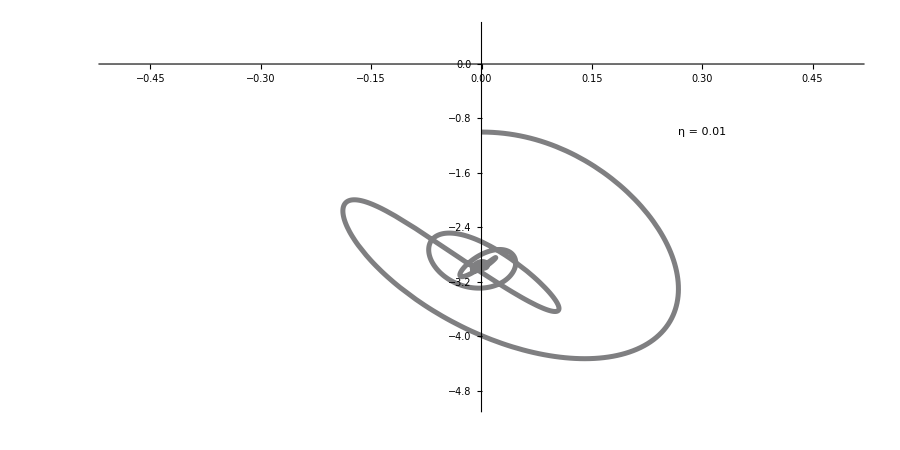

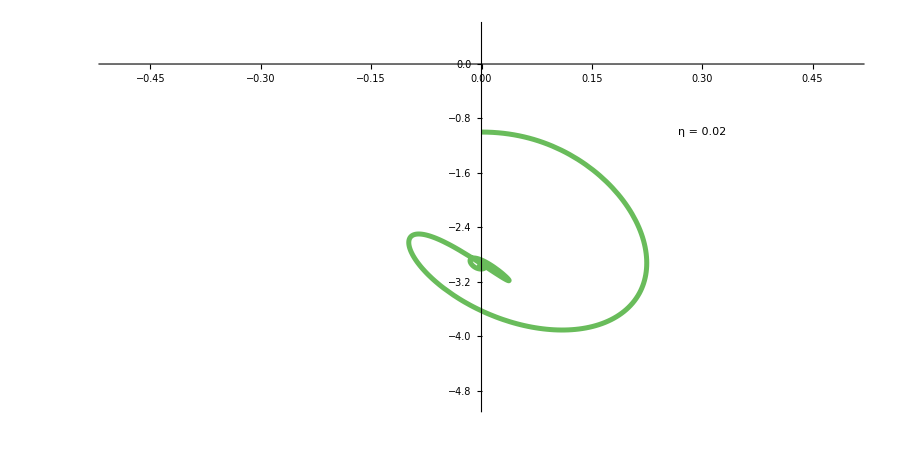

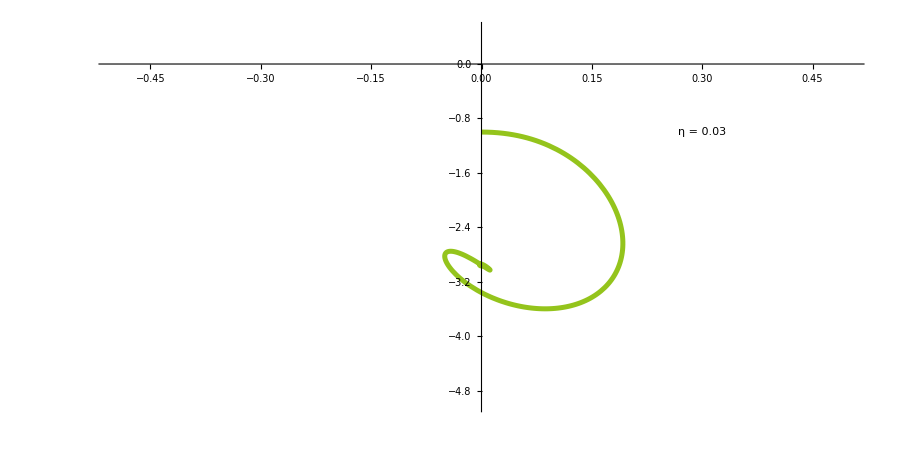

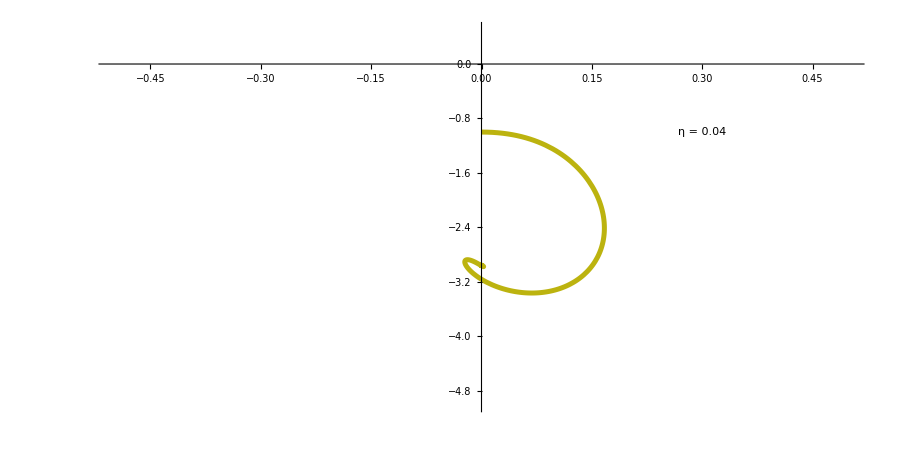

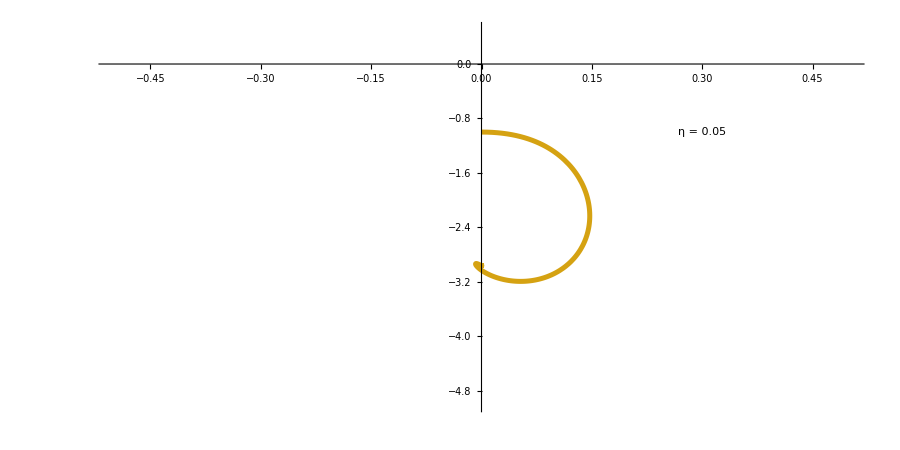

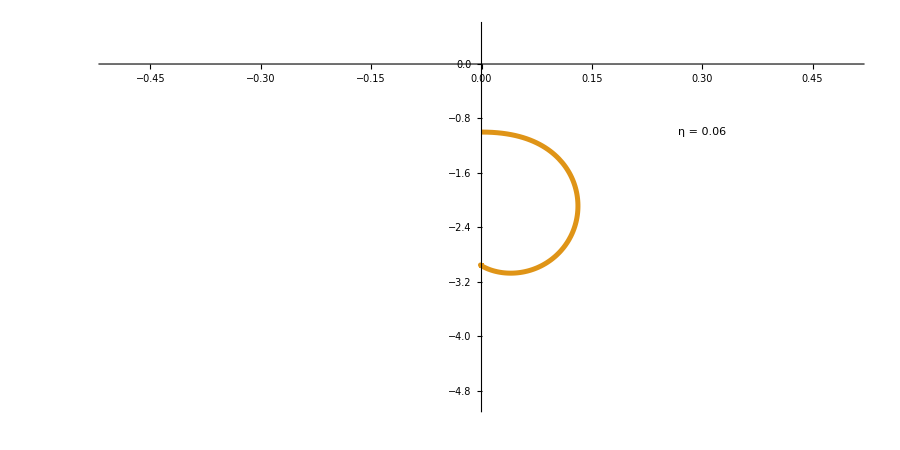

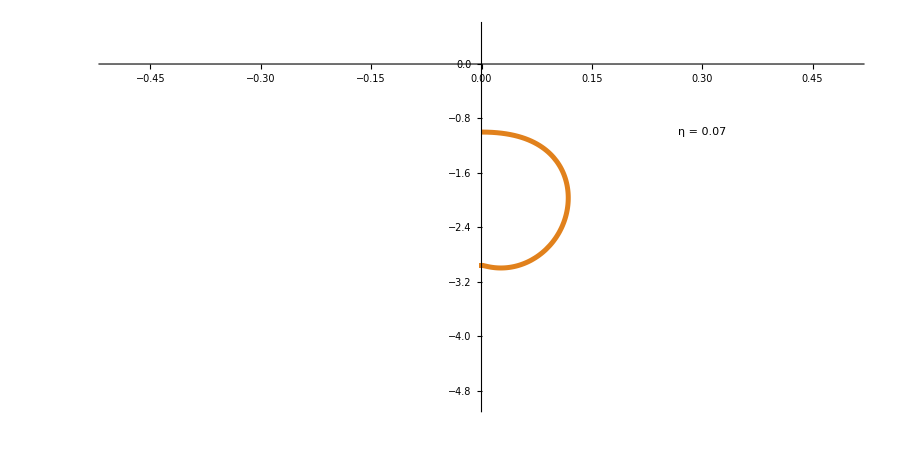

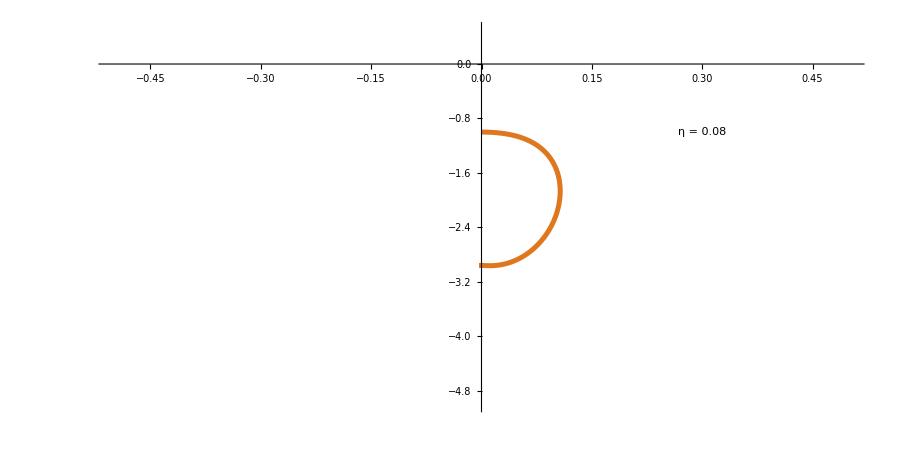

```mathematica
g=9.8;k=0.1;m=0.02;L0=1;tm=50;
xinitial={0,0.5};yinitial={-L0,0};
Do[equs=
{m x''[t]==-k x[t] (1-L0/(√(x[t]^2+y[t]^2)))-η x'[t],
m y''[t]==k y[t] (-1+L0/(√(x[t]^2+y[t]^2)))-m g-η y'[t],
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm}];
{x,y}={x,y}/.s[[1]];
p=ParametricPlot[{x[t],y[t]},{t,0,tm},
PlotRange->{{-0.5,0.5},{-5,0.5}},
AspectRatio->0.5,
Epilog->Text["η = "<>ToString[η],{0.3,-1}],
PlotStyle->Thickness[0.004],ColorFunction->Function[{x,y,t},Hue[t]]];
Print[p];Clear[x,y],
{η,0.01,0.2,0.01}]
Clear[g,k,m,L0,tm,equs,s,x,y,p]
```